## (#X): Static Quantities:

### (#X.1): CFFS |

```mathematica
Realℋ=-0.897;
RealℋT=2.444;
Realℰ=-0.541;
RealℰT=2.207;
Imaginaryℋ=2.421;
ImaginaryℋT=1.131;
Imaginaryℰ=0.903;
ImaginaryℰT=5.383;
ℋ=Realℋ+I Imaginaryℋ;
ℋT=RealℋT+I ImaginaryℋT;
ℰ=Realℰ+I Imaginaryℰ;
ℰT=RealℰT+I ImaginaryℰT;
```

## (#X): Substitutions:

### (#X.1): Kinematic Point 1 | “The Standard One”

```mathematica
kinematicSetting1={
y->0.49624,
M->0.938,
Q->Sqrt[1.82],
t->-0.17,
xB->0.34,
Subscript[α, EM]->1/137.036};
```

### (#X.2): Lightcone Choice | BKM:

```mathematica
lightconeBKMSetting={α->1/2,β->1/2};
```

### (#X.3): Lightcone Choice | UVA:

```mathematica
lightconeBKMSetting={α->1,β->1};
```

## h^U:

```mathematica
hU=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*ComplexConjugate[𝒯1[α3,α1]]*𝒯1[α4,α2]*(-MT[α3,α4])]]]//TraditionalForm
```

1/(2 M xB y^2 (Q^2+t)^2 (4 M^2 xB^2+Q^2)^2)Q^2 (8 M xB cos^2(ϕ) (Q^4 (M^2 xB^2-t xB+t)+Q^2 t xB (2 M^2 xB-t xB+t)+M^2 t^2 xB^2) (M^2 xB^2 y^2+Q^2 (y-1))+4 Q^5 (y-2) cos(ϕ) √((4 M^2 xB^2)/Q^2+1) (Q^4+Q^2 t (3 xB-1)+t^2 xB (2 xB-1)) √(-(M^2 xB^2 (Q^4 (M^2 xB^2-t xB+t)+Q^2 t xB (2 M^2 xB-t xB+t)+M^2 t^2 xB^2))/((4 M^2 xB^2+Q^2) (Q^3+Q t xB)^2)) √(-(M^2 xB^2 y^2)/Q^2-y+1)+M xB (8 M^4 t^2 xB^4 y^2+2 Q^6 (2 M^2 xB^2 y^2+t xB (y-2)^2+2 t (y-1))+4 M^2 Q^2 t xB^2 y^2 (4 M^2 xB^2+t)+Q^4 (8 M^4 xB^4 y^2+8 M^2 t xB^2 y^2+t^2 (2 xB^2 (y-2)^2-2 xB (y-2)^2+y^2-2 y+2))+Q^8 (y^2-2 y+2)))

## h^UTilde

```mathematica
hUTilde=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*ComplexConjugate[𝒯1t[α3,α1]]*𝒯1t[α4,α2]*(-MT[α3,α4])]]] //TraditionalForm
```

1/(2 M xB y^2 (Q^2+t)^2 (4 M^2 xB^2+Q^2)^2)Q^2 (8 M xB cos^2(ϕ) (Q^4 (M^2 xB^2-t xB+t)+Q^2 t xB (2 M^2 xB-t xB+t)+M^2 t^2 xB^2) (M^2 xB^2 y^2+Q^2 (y-1))+4 Q^5 (y-2) cos(ϕ) √((4 M^2 xB^2)/Q^2+1) (Q^4+Q^2 t (3 xB-1)+t^2 xB (2 xB-1)) √(-(M^2 xB^2 (Q^4 (M^2 xB^2-t xB+t)+Q^2 t xB (2 M^2 xB-t xB+t)+M^2 t^2 xB^2))/((4 M^2 xB^2+Q^2) (Q^3+Q t xB)^2)) √(-(M^2 xB^2 y^2)/Q^2-y+1)+M xB (8 M^4 t^2 xB^4 y^2+2 Q^6 (2 M^2 xB^2 y^2+t xB (y-2)^2+2 t (y-1))+4 M^2 Q^2 t xB^2 y^2 (4 M^2 xB^2+t)+Q^4 (8 M^4 xB^4 y^2+8 M^2 t xB^2 y^2+t^2 (2 xB^2 (y-2)^2-2 xB (y-2)^2+y^2-2 y+2))+Q^8 (y^2-2 y+2)))

## h^(-,L)

```mathematica
hMinusL=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*-ⅈ/2(𝒯1[α3,α1]*𝒯1t[α4,α2]+𝒯1t[α3,α1]*𝒯1[α4,α2])*(-MT[α3,α4])]]]//TraditionalForm
```

0

## h^(+,U)

```mathematica
hPlusU=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*-ⅈ/2(𝒯1[α3,α1]*𝒯1t[α4,α2]-𝒯1t[α3,α1]*𝒯1[α4,α2])*(-MT[α3,α4])]]] //TraditionalForm
```

(Q^4 (y-2) (Q^2+t (2 xB-1)))/(2 y √((Q^2+t)^2) (4 M^2 xB^2+Q^2))+(2 Q^3 cos(ϕ) (Q^2+t xB) √(-(M^2 xB^2 (Q^4 (M^2 xB^2-t xB+t)+Q^2 t xB (2 M^2 xB-t xB+t)+M^2 t^2 xB^2))/((4 M^2 xB^2+Q^2) (Q^3+Q t xB)^2)) √(-(M^2 xB^2 y^2)/Q^2-y+1))/(M xB y √((Q^2+t)^2) √((4 M^2 xB^2)/Q^2+1))

## F_UU

```mathematica
Fuu = 4((1-ξ^2)(hU Conjugate[ℋ] ℋ + hUTilde Conjugate[ℋT ] ℋT )-t/(4 M^2)(hU Conjugate[ℰ]ℰ+ ξ^2 hUTilde Conjugate[ℰT] ℰT  )-ξ^2(hU Conjugate[ℰ] ℰ + hU(Conjugate[ℰ] ℋ+Conjugate[ℋ] ℰ)+hUTilde )(Conjugate[ℰT] ℋT + Conjugate[ℋT] ℰT));
```

```mathematica
Fuu/.ξsub/.lightconeBKMSetting/.kinematicSetting1
```

(29.0362+0. ⅈ) (0.858282 (0.18872 cos^2(ϕ)-1.77982 cos(ϕ)+4.72652))

## (#X): Plots:

## (#X.1): Pure DVCS:

#### (#X.1.1): Pure DVCS | Unpolarized Beam | Unpolarized Target:

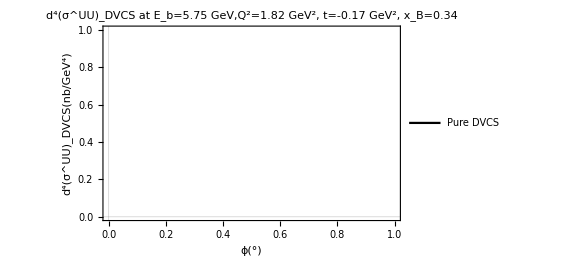

```mathematica
Plot[Fuu/.ξsub/.lightconeBKMSetting/.kinematicSetting1/.ϕ->ϕp/180*π,
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"Pure DVCS"},
LegendLayout->{"Row",2}
],
{0.85,0.85}],
ImageSize->Automatic,
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^UU)_DVCS(nb/GeV^4)"},
PlotStyle->{Black},
PlotLabel->"d^4(σ^UU)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->All,
PlotTheme -> "Scientific"]
```